```mathematica
jsonTemplateFilename="~/projects/elixir/gelid/gelid/data/mathematica-json-template.txt"
```

~/projects/elixir/gelid/gelid/data/mathematica-json-template.txt

```mathematica
"~/projects/elixir/gelid/gelid/data/mathematica-json-template.txt"
```

~/projects/elixir/gelid/gelid/data/mathematica-json-template.txt

```mathematica
experiment=<|
"domain"->{{0.2,0.1},{0.1,0.1},{0.1,0.2}},
"population"->{
<|"route"->{1,0,2},"age"->2,"score"->2.5|>,
<|"route"->{0,2,1},"age"->3,"score"->2.1|>,
<|"route"->{2,1,0},"age"->1,"score"->3.5|>
}
|>
```

<|domain→{{0.2,0.1},{0.1,0.1},{0.1,0.2}},population→{<|route→{1,0,2},age→2,score→2.5|>,<|route→{0,2,1},age→3,score→2.1|>,<|route→{2,1,0},age→1,score→3.5|>}|>

```mathematica
Export[jsonTemplateFilename, experiment, "JSON"]
```

~/projects/elixir/gelid/gelid/data/mathematica-json-template.txt

```mathematica
testRead=Association[Import[jsonTemplateFilename,"JSON"]]
```

<|domain→{{0.2,0.1},{0.1,0.1},{0.1,0.2}},population→{{route→{1,0,2},age→2,score→2.5},{route→{0,2,1},age→3,score→2.1},{route→{2,1,0},age→1,score→3.5}}|>

```mathematica
experiment["domain"]
```

{{0.2,0.1},{0.1,0.1},{0.1,0.2}}

```mathematica
testRead["population"]
```

{{route→{1,0,2},age→2,score→2.5},{route→{0,2,1},age→3,score→2.1},{route→{2,1,0},age→1,score→3.5}}

```mathematica
dataRead=Association[Import["~/projects/elixir/gelid/gelid/data/20230217005445Z-999.json","JSON"]]
```

```mathematica
cityPositions=dataRead["domain"]
```

{{0.499184,0.818892},{0.584941,0.556767},{0.52077,0.671441},{0.432003,0.553088},{0.509728,0.926562},{0.865617,0.230826},{0.585129,0.113663},{0.740343,0.040954},{0.444913,0.392326},{0.203472,0.876972},{0.157773,0.289789},{0.753798,0.683961},{0.879319,0.906758},{0.182714,0.515244},{0.315957,0.00216706},{0.954825,0.644141},{0.371351,0.197023},{0.68799,0.241298},{0.382983,0.181627},{0.831751,0.486156},{0.859327,0.798594},{0.640626,0.847862},{0.769807,0.747114},{0.740843,0.959079},{0.727546,0.804303},{0.691173,0.217954},{0.807363,0.969883},{0.224306,0.65266},{0.208374,0.596681},{0.283901,0.90087},{0.493383,0.550444},{0.0402559,0.922326},{0.353977,0.734528},{0.508954,0.0242263},{0.643312,0.58851},{0.240463,0.571932},{0.287557,0.41841},{0.632963,0.433555},{0.804724,0.177795},{0.674552,0.282464},{0.421442,0.875152},{0.68794,0.580614},{0.441486,0.151525},{0.800482,0.498449},{0.209755,0.91712},{0.212376,0.907623},{0.823116,0.689667},{0.44523,0.487129},{0.746676,0.604395},{0.415568,0.708932},{0.0478748,0.0390902},{0.664877,0.350482},{0.885242,0.353798},{0.510407,0.0315595},{0.299189,0.894025},{0.629098,0.295297},{0.951627,0.785174},{0.558038,0.728744},{0.759658,0.225702},{0.673132,0.474437},{0.960854,0.049858},{0.0199971,0.189457},{0.852236,0.391066},{0.824496,0.222131},{0.0661645,0.16145},{0.378287,0.555545},{0.0239899,0.0438665},{0.227995,0.582436},{0.135216,0.879764},{0.941775,0.876751},{0.899581,0.0150464},{0.928796,0.844884},{0.746285,0.638173},{0.486407,0.620975},{0.283987,0.58029},{0.143097,0.313751},{0.00683116,0.120786},{0.116641,0.318375},{0.294461,0.134106},{0.278741,0.118689},{0.166337,0.7471},{0.466615,0.830699},{0.731219,0.452669},{0.273319,0.971108},{0.678951,0.100784},{0.278576,0.0525386},{0.799372,0.190241},{0.47828,0.363379},{0.386052,0.111051},{0.559302,0.288049},{0.932377,0.930114},{0.219499,0.134452},{0.285451,0.140018},{0.61043,0.383716},{0.378584,0.398667},{0.0265232,0.924511},{0.673998,0.73279},{0.689851,0.786419},{0.230585,0.254334},{0.67301,0.284862}}

```mathematica
population=DeleteDuplicates[Map[Association,dataRead["population"]]]
```

{<|age→0,score→113.736,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,79,14,33,51,41,7,84,52,46,20,23,4,83,68,21,57,49,69,56,15,98,61,66,85,50,6,38,86,25,58,78,18,89,87,35,28,81,97}|>,<|age→0,score→113.7,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,79,14,33,51,41,7,84,52,46,20,23,4,83,68,21,57,49,69,56,15,98,61,66,85,50,6,38,86,25,58,78,18,89,87,28,35,81,97}|>,<|age→0,score→113.314,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,79,14,33,51,41,7,84,52,46,20,23,4,83,68,21,57,49,69,56,15,98,61,66,85,50,6,38,86,25,58,78,18,89,87,81,28,35,97}|>,<|age→0,score→113.08,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,79,14,33,51,41,7,84,52,46,20,23,4,83,68,21,57,49,69,56,15,98,78,61,85,50,6,38,86,25,58,66,18,89,87,35,28,81,97}|>,<|age→0,score→112.863,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,79,14,33,51,41,7,84,52,46,20,23,4,83,68,21,57,49,69,56,15,98,61,66,85,50,6,38,86,25,58,35,18,89,87,78,28,81,97}|>,<|age→0,score→112.785,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,33,64,92,88,53,42,75,10,79,14,35,51,41,7,84,52,46,20,23,4,83,68,21,57,49,69,56,15,98,61,66,85,50,6,38,86,25,58,78,18,89,87,36,28,81,97}|>,<|age→0,score→112.747,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,44,16,8,2,80,31,40,43,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,79,14,33,51,41,7,84,52,46,20,23,4,83,68,21,57,49,69,56,15,98,61,66,85,50,6,38,86,25,58,78,18,89,87,35,28,81,97}|>,<|age→0,score→112.384,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,79,14,33,51,41,7,84,52,46,20,23,4,83,68,21,57,49,69,56,15,98,61,66,85,50,6,38,86,25,58,78,18,28,89,81,35,87,97}|>,<|age→0,score→112.107,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,79,14,33,51,41,7,84,52,46,20,23,4,83,68,21,57,49,69,56,15,98,61,66,78,50,6,38,86,25,58,81,18,89,87,35,28,85,97}|>,<|age→0,score→112.018,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,79,14,33,51,41,7,84,52,46,20,23,4,83,68,21,57,49,69,56,15,98,61,66,85,50,6,38,86,25,81,58,18,89,87,35,28,78,97}|>,<|age→0,score→111.849,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,79,14,33,51,41,7,84,52,46,20,23,4,83,68,21,57,49,69,56,15,98,61,66,50,58,6,38,86,25,78,81,18,89,87,35,28,85,97}|>,<|age→0,score→111.658,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,79,14,33,51,41,7,84,49,46,20,23,4,83,68,21,57,50,69,56,15,98,61,66,85,52,6,38,86,25,58,78,18,89,87,35,28,81,97}|>,<|age→0,score→111.51,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,23,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,79,14,33,51,41,7,84,52,46,20,25,4,83,68,21,57,49,69,56,15,98,61,66,85,50,6,38,86,26,58,78,18,89,87,35,28,81,97}|>,<|age→0,score→110.914,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,84,14,33,51,41,7,83,52,46,20,23,4,81,68,21,57,49,69,56,15,98,61,66,85,50,6,38,86,25,58,78,18,89,87,35,28,79,97}|>,<|age→0,score→108.878,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,49,92,88,56,42,75,10,79,14,33,52,41,7,84,53,46,20,23,4,83,68,21,58,50,69,57,15,98,64,66,85,51,6,38,86,25,61,78,18,89,87,35,28,81,97}|>,<|age→0,score→108.821,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,57,14,33,51,41,7,84,52,46,20,23,4,83,69,21,58,49,78,56,15,98,66,68,85,50,6,38,86,25,61,79,18,89,87,35,28,81,97}|>,<|age→0,score→108.659,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,44,91,76,3,67,43,16,8,2,80,31,40,45,95,65,27,32,94,74,13,9,55,73,1,49,90,71,26,29,46,0,63,5,60,70,12,77,36,64,92,88,54,42,75,10,79,14,33,52,41,7,84,53,48,20,23,4,83,68,21,57,50,69,56,15,98,61,66,85,51,6,38,86,25,58,78,18,89,87,35,28,81,97}|>,<|age→0,score→108.46,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,20,2,80,31,40,44,95,65,27,32,94,74,12,8,54,73,1,48,90,71,26,29,45,0,63,5,60,70,10,77,36,64,92,88,53,42,75,9,79,13,33,51,41,7,84,52,46,18,23,4,83,68,21,57,49,69,56,14,98,61,66,85,50,6,38,86,25,58,78,15,89,87,35,28,81,97}|>,<|age→0,score→108.196,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,75,27,32,94,73,13,9,54,71,1,48,90,70,26,29,45,0,63,5,60,69,12,77,36,64,92,88,53,42,74,10,79,14,33,51,41,7,84,52,46,20,23,4,83,66,21,57,49,68,56,15,98,61,65,85,50,6,38,86,25,58,78,18,89,87,35,28,81,97}|>,<|age→0,score→106.514,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,33,14,35,52,46,7,84,56,49,20,23,4,83,69,21,58,50,78,57,15,98,66,68,85,51,6,41,86,25,61,79,18,89,87,38,28,81,97}|>,<|age→0,score→106.251,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,79,14,33,51,81,7,84,50,41,20,23,4,83,66,21,56,46,68,52,15,98,58,61,85,49,6,38,86,25,57,69,18,89,87,35,28,78,97}|>,<|age→0,score→105.991,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,85,69,12,75,36,61,92,88,53,42,70,10,78,14,33,51,41,7,83,52,46,20,23,4,81,66,21,57,49,68,56,15,98,60,64,84,50,6,38,86,25,58,77,18,89,87,35,28,79,97}|>,<|age→0,score→104.992,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,56,13,9,54,74,1,48,90,73,26,29,45,0,64,5,61,71,12,77,36,66,92,88,53,42,75,10,79,14,33,51,41,7,84,52,46,20,23,4,83,69,21,58,49,70,57,15,98,63,68,85,50,6,38,86,25,60,78,18,89,87,35,28,81,97}|>,<|age→0,score→104.734,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,15,95,65,28,33,94,74,13,9,54,73,1,48,90,71,27,32,45,0,63,5,60,70,12,77,38,64,92,88,53,44,75,10,79,14,35,51,42,7,84,52,46,21,25,4,83,68,23,57,49,69,56,18,98,61,66,85,50,6,41,86,26,58,78,20,89,87,36,29,81,97}|>,<|age→0,score→104.526,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,15,38,66,92,88,56,46,77,10,79,14,35,52,42,7,84,53,49,21,25,4,83,69,23,58,50,75,57,18,98,64,68,85,51,6,41,86,28,61,78,20,89,87,36,33,81,97}|>,<|age→0,score→103.535,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,26,29,45,0,63,5,60,70,12,77,36,64,92,88,53,42,75,10,79,14,33,51,41,7,21,56,49,20,25,4,84,69,23,58,50,78,57,15,98,66,68,85,52,6,46,86,28,61,81,18,89,87,38,35,83,97}|>,<|age→0,score→103.454,route→{62,19,11,72,37,60,30,24,82,17,93,96,99,38,58,22,46,54,91,76,3,67,42,16,8,2,80,31,39,43,95,65,27,32,94,74,13,9,53,73,1,47,90,71,26,29,44,0,63,5,59,70,12,77,35,64,92,88,52,41,75,10,79,14,33,50,40,7,84,51,45,20,23,4,83,68,21,56,48,69,55,15,98,61,66,85,49,6,36,86,25,57,78,18,89,87,34,28,81,97}|>,<|age→0,score→102.661,route→{62,19,11,72,37,34,30,24,82,17,93,96,67,39,59,22,47,55,92,77,3,68,43,16,8,2,81,31,40,44,97,65,27,32,95,75,13,9,54,74,1,48,91,73,26,29,45,0,63,5,60,71,12,78,36,64,94,89,53,42,76,10,80,14,33,51,41,7,85,52,46,20,23,4,84,69,21,57,49,70,56,15,99,61,66,86,50,6,38,87,25,58,79,18,90,88,35,28,83,98}|>,<|age→0,score→102.274,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,27,28,33,94,74,13,9,56,73,1,49,90,71,26,32,46,0,64,5,61,70,12,77,38,65,92,88,54,45,75,10,79,14,35,52,42,7,84,53,48,20,23,4,83,68,21,58,50,69,57,15,98,63,66,85,51,6,41,86,25,60,78,18,89,87,36,29,81,97}|>,<|age→0,score→101.655,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,68,42,95,64,27,32,94,74,13,9,53,73,1,46,90,71,26,29,44,0,61,5,58,70,12,77,36,63,92,88,52,41,75,10,79,14,33,50,40,7,84,51,45,20,23,4,83,66,21,56,48,69,54,15,98,60,65,85,49,6,38,86,25,57,78,18,89,87,35,28,81,97}|>,<|age→0,score→101.536,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,48,90,71,66,28,42,0,61,5,58,70,12,77,35,63,92,88,52,41,75,10,79,14,29,50,38,7,84,51,45,20,23,4,83,68,21,56,46,69,53,15,98,60,64,85,49,6,36,86,25,57,78,18,89,87,33,26,81,97}|>,<|age→0,score→101.466,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,67,43,16,8,2,80,31,40,44,95,65,27,32,94,74,13,9,54,73,1,81,90,70,26,29,45,0,61,5,58,69,12,75,36,63,92,88,52,42,71,10,78,14,33,50,41,7,84,51,46,20,23,4,83,66,21,56,48,68,53,15,98,60,64,85,49,6,38,86,25,57,77,18,89,87,35,28,79,97}|>,<|age→0,score→100.353,route→{62,59,11,72,36,33,29,23,82,17,93,96,99,38,58,21,46,54,91,76,3,67,42,16,8,2,80,30,39,43,95,65,26,31,94,74,13,9,53,73,1,47,90,71,25,28,44,0,63,5,60,70,12,77,35,64,92,88,52,41,75,10,79,14,32,50,40,7,84,51,45,19,22,4,83,68,20,56,48,69,55,15,98,61,66,85,49,6,37,86,24,57,78,18,89,87,34,27,81,97}|>,<|age→0,score→100.131,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,76,54,91,75,3,66,43,16,8,2,80,31,40,44,95,64,27,32,94,73,13,9,53,71,1,47,90,70,26,29,45,0,61,5,58,69,12,77,36,63,92,88,52,42,74,10,79,14,33,50,41,7,84,51,46,20,23,4,83,67,21,56,48,68,55,15,98,60,65,85,49,6,38,86,25,57,78,18,89,87,35,28,81,97}|>,<|age→0,score→100.13,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,91,76,3,38,44,16,8,2,80,31,41,45,95,66,27,32,94,74,13,9,56,73,1,49,90,71,26,29,46,0,64,5,61,70,12,77,36,65,92,88,54,43,75,10,79,14,33,52,42,7,84,53,48,20,23,4,83,68,21,58,50,69,57,15,98,63,67,85,51,6,40,86,25,60,78,18,89,87,35,28,81,97}|>,<|age→0,score→97.7882,route→{62,19,11,72,37,34,71,24,82,17,93,96,99,38,58,22,46,54,91,76,3,66,42,16,8,2,80,30,39,43,95,64,27,31,94,74,13,9,53,73,1,47,90,70,26,29,44,0,61,5,59,69,12,77,35,63,92,88,52,41,75,10,79,14,32,50,40,7,84,51,45,20,23,4,83,67,21,56,48,68,55,15,98,60,65,85,49,6,36,86,25,57,78,18,89,87,33,28,81,97}|>,<|age→0,score→97.3393,route→{62,19,11,72,37,34,30,24,82,17,93,96,99,39,59,22,47,55,54,77,3,68,43,16,8,2,81,31,40,44,95,66,27,32,94,75,13,9,56,74,1,48,91,73,26,29,45,0,64,5,61,71,12,78,36,65,92,89,53,42,76,10,80,14,33,51,41,7,85,52,46,20,23,4,84,69,21,58,49,70,57,15,98,63,67,86,50,6,38,87,25,60,79,18,90,88,35,28,83,97}|>,<|age→0,score→93.698,route→{62,19,11,72,37,34,30,24,82,17,25,96,99,40,60,22,48,56,92,77,3,68,44,16,8,2,81,32,41,45,95,66,28,33,94,75,13,9,55,74,1,49,91,73,27,31,46,0,64,5,61,71,12,78,38,65,93,89,54,43,76,10,80,14,35,52,42,7,85,53,47,20,23,4,84,69,21,58,50,70,57,15,98,63,67,86,51,6,39,87,26,59,79,18,90,88,36,29,83,97}|>,<|age→0,score→91.7609,route→{62,19,11,72,37,34,30,96,81,17,92,95,99,38,58,22,46,54,90,75,3,66,42,16,8,2,79,29,39,43,94,64,26,31,93,73,13,9,53,71,1,47,89,70,25,28,44,0,61,5,59,69,12,76,35,63,91,87,52,41,74,10,78,14,32,50,40,7,83,51,45,20,23,4,82,67,21,56,48,68,55,15,98,60,65,84,49,6,36,85,24,57,77,18,88,86,33,27,80,97}|>}

```mathematica
census=Length[population]
scores=Map[#["score"]&, population];
sum=Fold[Plus, 0, scores]
mean=sum/census
max=Max[scores]
min=Min[scores]
(min+max)/2
```

39

4148.47

106.371

113.736

91.7609

102.748

```mathematica
route=cityPositions
ListLinePlot[Map[route[#]&,First[population]["route"]], AspectRatio->1]
```

{{0.499184,0.818892},{0.584941,0.556767},{0.52077,0.671441},{0.432003,0.553088},{0.509728,0.926562},{0.865617,0.230826},{0.585129,0.113663},{0.740343,0.040954},{0.444913,0.392326},{0.203472,0.876972},{0.157773,0.289789},{0.753798,0.683961},{0.879319,0.906758},{0.182714,0.515244},{0.315957,0.00216706},{0.954825,0.644141},{0.371351,0.197023},{0.68799,0.241298},{0.382983,0.181627},{0.831751,0.486156},{0.859327,0.798594},{0.640626,0.847862},{0.769807,0.747114},{0.740843,0.959079},{0.727546,0.804303},{0.691173,0.217954},{0.807363,0.969883},{0.224306,0.65266},{0.208374,0.596681},{0.283901,0.90087},{0.493383,0.550444},{0.0402559,0.922326},{0.353977,0.734528},{0.508954,0.0242263},{0.643312,0.58851},{0.240463,0.571932},{0.287557,0.41841},{0.632963,0.433555},{0.804724,0.177795},{0.674552,0.282464},{0.421442,0.875152},{0.68794,0.580614},{0.441486,0.151525},{0.800482,0.498449},{0.209755,0.91712},{0.212376,0.907623},{0.823116,0.689667},{0.44523,0.487129},{0.746676,0.604395},{0.415568,0.708932},{0.0478748,0.0390902},{0.664877,0.350482},{0.885242,0.353798},{0.510407,0.0315595},{0.299189,0.894025},{0.629098,0.295297},{0.951627,0.785174},{0.558038,0.728744},{0.759658,0.225702},{0.673132,0.474437},{0.960854,0.049858},{0.0199971,0.189457},{0.852236,0.391066},{0.824496,0.222131},{0.0661645,0.16145},{0.378287,0.555545},{0.0239899,0.0438665},{0.227995,0.582436},{0.135216,0.879764},{0.941775,0.876751},{0.899581,0.0150464},{0.928796,0.844884},{0.746285,0.638173},{0.486407,0.620975},{0.283987,0.58029},{0.143097,0.313751},{0.00683116,0.120786},{0.116641,0.318375},{0.294461,0.134106},{0.278741,0.118689},{0.166337,0.7471},{0.466615,0.830699},{0.731219,0.452669},{0.273319,0.971108},{0.678951,0.100784},{0.278576,0.0525386},{0.799372,0.190241},{0.47828,0.363379},{0.386052,0.111051},{0.559302,0.288049},{0.932377,0.930114},{0.219499,0.134452},{0.285451,0.140018},{0.61043,0.383716},{0.378584,0.398667},{0.0265232,0.924511},{0.673998,0.73279},{0.689851,0.786419},{0.230585,0.254334},{0.67301,0.284862}}

-Graphics-

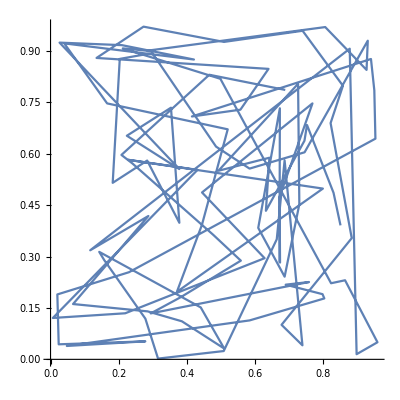

```mathematica
First[population]["route"];
Map[cityPositions[[#+1]]&,%];
ListLinePlot[%, AspectRatio->1]
```